# Chapter 3: Climate and Weather Analysis

Climate and weather datasets form the backbone of Earth observation science. Google Earth Engine hosts decades of satellite-derived temperature, precipitation, atmospheric, and radiation products at global scales. This chapter demonstrates how to extract, process, and analyze these datasets using the GoogleEarthEngineClient paclet alongside Wolfram Language's built-in statistical and time series tools.

Every example follows a consistent pattern: build a server-side processing pipeline with the // operator, retrieve the result with GEECompute, GEEIdentify, or GEEComputePixels, then analyze client-side with Wolfram Language functions such as TimeSeries, LinearModelFit, MovingAverage, and DateListPlot.

Prerequisite: Authenticate per Section 1.3 and load the paclet with Needs["GoogleEarthEngineClient`"].

## 3.1 Surface Temperature

Land surface temperature (LST) is a fundamental climate variable that governs surface energy balance, evapotranspiration, and urban comfort. Two complementary satellite products provide LST at different spatial and temporal resolutions.

## 3.1.1 MODIS Land Surface Temperature

The MODIS/061/MOD11A2 product delivers 8-day composite LST at 1 km resolution. Raw pixel values are stored as scaled integers; multiply by 0.02 to convert to Kelvin, then subtract 273.15 to obtain degrees Celsius.

Map daytime LST over a city to reveal the urban heat island effect:

```mathematica
(* Build a summer LST composite for Phoenix, Arizona *)
loc=GeoCircle[,Quantity[50,"Kilometers"]];
lstExpr = GEECollection["MODIS/061/MOD11A2"] //
  GEEFilterDate["2024-06-01", "2024-09-01"] //
  GEEFilterBounds[loc] //
  GEESelectBands[{"LST_Day_1km"}] //
  GEEMean //
  GEEMultiply[0.02] //
  GEEAdd[-273.15];

(* Render as a color-mapped temperature image *)
lstImage = GEEComputePixels[loc, lstExpr,
  "VisParams" -> <|"min" -> 35, "max" -> 55,
    "palette" -> {"#2166ac", "#67a9cf", "#d1e5f0",
      "#fddbc7", "#ef8a62", "#b2182b"}|>,
  "ImageSize" -> {512, 512}]
(* Blue = cooler parks and irrigated areas, red = hot impervious surfaces *)
```

-Graphics-

The scale factor pipeline (GEEMultiply[0.02] // GEEAdd[-273.15]) runs entirely server-side, so you receive physically meaningful Celsius values without downloading raw integers.

Query LST at specific points across the urban-rural gradient:

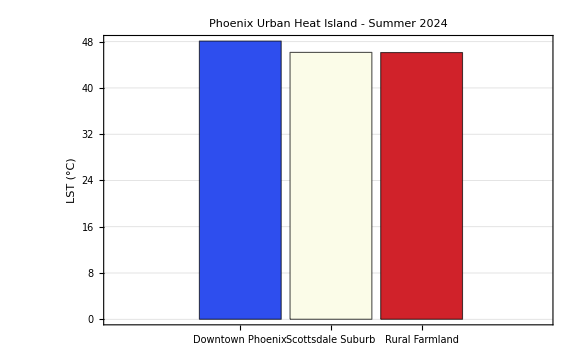

```mathematica
(* Define points: downtown, suburb, agricultural fringe *)
points = <|
  "Downtown Phoenix" -> GeoPosition[{33.45, -112.07}],
  "Scottsdale Suburb" -> GeoPosition[{33.50, -111.93}],
  "Rural Farmland" -> GeoPosition[{33.38, -112.25}]
|>;

lstResults = Association @ KeyValueMap[
  Function[{name, pos},
    name -> GEEIdentify[pos, lstExpr]["Values"][[1]]
  ],
  points
];

BarChart[lstResults,
  ChartLabels -> Keys[lstResults],
  AxesLabel -> {None, "LST (°C)"},
  PlotLabel -> "Phoenix Urban Heat Island - Summer 2024",
  ChartStyle -> "TemperatureMap",
ImageSize->Large,
PlotTheme->"Detailed"]
(* Downtown typically 5-10°C warmer than surrounding farmland *)
```

## 3.1.2 Landsat Thermal Band

Landsat 8 Collection 2 Level 2 provides surface temperature via the ST_B10 band at 30 m resolution -- much finer than MODIS. This enables intra-urban thermal comparisons between parks and built-up areas. For the Landsat thermal scale factors and band conventions, see Section 2.2. For urban heat island analysis using these thermal products, see Section 7.2.

Compare LST between an urban park and its surroundings:

```mathematica
(* Cloud-filtered Landsat 8 surface temperature for Austin, TX *)
landsatLST = GEECollection["LANDSAT/LC08/C02/T1_L2"] //
  GEEFilterDate["2024-06-01", "2024-09-01"] //
  GEEFilterBounds[{-97.8, 30.2, -97.7, 30.35}] //
  GEEFilterProperty["CLOUD_COVER", "LessThan", 20] //
  GEESelectBands[{"ST_B10"}] //
  GEEMedian //
  GEEMultiply[0.00341802] //
  GEEAdd[149.0 - 273.15];

(* Sample at multiple points: Zilker Park vs. downtown *)
parkPoints = {
  GeoPosition[{30.267, -97.773}],  (* Zilker Park center *)
  GeoPosition[{30.271, -97.770}],  (* Zilker Park edge *)
  GeoPosition[{30.264, -97.776}]   (* Barton Springs *)
};
urbanPoints = {
  GeoPosition[{30.267, -97.743}],  (* Congress Avenue *)
  GeoPosition[{30.270, -97.740}],  (* East 6th Street *)
  GeoPosition[{30.265, -97.747}]   (* Rainey Street *)
};

parkTemps = Mean[
  First /@ (#["Values"] & /@ GEEGetSamples[parkPoints, landsatLST])];
urbanTemps = Mean[
  First /@ (#["Values"] & /@ GEEGetSamples[urbanPoints, landsatLST])];

Grid[{
  {"Location", "Mean LST (°C)"},
  {"Zilker Park", Round[parkTemps, 0.1]},
  {"Downtown", Round[urbanTemps, 0.1]},
  {"Difference", Round[urbanTemps - parkTemps, 0.1]}
}, Frame -> All]
```

Location | Mean LST (°C)
Zilker Park | 38.5
Downtown | 41.
Difference | 2.5

## 3.1.3 Satellite vs. Ground Station Validation

Comparing satellite-derived LST with ground-based air temperature helps establish confidence in the remote sensing product. Note that LST (skin temperature) and air temperature (measured at ~2 m height) differ physically, so systematic offsets are expected.

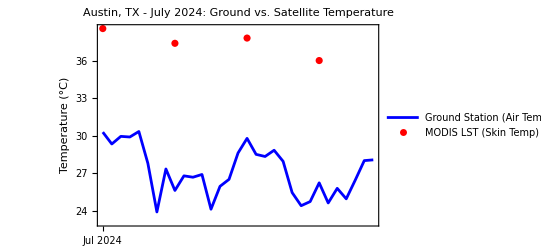

```mathematica
(* Wolfram Language ground station data for Austin, July 2024 *)
groundTemp = WeatherData["Austin", "Temperature",
  {{2024, 7, 1}, {2024, 7, 31}, "Day"}];

(* GEE satellite LST at the Austin weather station location *)
stationPos = GeoPosition[{30.30, -97.70}];
satelliteLST = Table[
  Module[{dateStr, endStr, expr, result},
    (* MOD11A2 is an 8-day composite; use an 8-day filter window
       aligned to composite start dates *)
    dateStr = DateString[{2024, 7, d}, {"Year", "-", "Month", "-", "Day"}];
    endStr = DateString[{2024, 7, d + 8}, {"Year", "-", "Month", "-", "Day"}];
    expr = GEECollection["MODIS/061/MOD11A2"] //
      GEEFilterDate[dateStr, endStr] //
      GEESelectBands[{"LST_Day_1km"}] //
      GEEMosaic //
      GEEMultiply[0.02] //
      GEEAdd[-273.15];
    result = GEEIdentify[stationPos, expr];
    If[result["Values"][[1]] === Null,
      Missing["NoData"],
      result["Values"][[1]]
    ]
  ],
  {d, 1, 28, 8}  (* 8-day intervals matching MODIS compositing *)
];

(* Build time series for both sources *)
modDates = Table[DateObject[{2024, 7, d}], {d, 1, 28, 8}];
satelliteTS = TimeSeries[
  DeleteCases[
    Transpose[{modDates, satelliteLST}],
    {_, _Missing}
  ]
];

(* Plot both on the same axis *)
DateListPlot[{groundTemp, satelliteTS},
  PlotLegends -> {"Ground Station (Air Temp)", "MODIS LST (Skin Temp)"},
  PlotLabel -> "Austin, TX - July 2024: Ground vs. Satellite Temperature",
  AxesLabel -> {None, "Temperature (°C)"},
  PlotStyle -> {Blue, Red},
  Joined -> {True, False},
  PlotMarkers -> {None, Automatic}]
(* LST is typically warmer than air temperature, especially on sunny days *)
```

## 3.2 Precipitation and Rainfall

Precipitation is the primary driver of hydrology, agriculture, and flood risk. Two complementary products provide global coverage at different resolutions.

## 3.2.1 CHIRPS Daily Rainfall

The Climate Hazards Group InfraRed Precipitation with Station data (CHIRPS) at UCSB-CHG/CHIRPS/DAILY provides daily rainfall at approximately 5 km resolution with records extending back to 1981. This long record makes it ideal for climatological analysis.

Monthly rainfall accumulation:

Summing daily images over one month gives total precipitation in millimeters. GEECollectionSum performs a pixel-wise sum across the entire filtered collection.

```mathematica
(* Total rainfall for July 2024 over the Indian monsoon region *)
julyRain = GEECollection["UCSB-CHG/CHIRPS/DAILY"] //
  GEEFilterDate["2024-07-01", "2024-08-01"] //
  GEEFilterBounds[{68.0, 8.0, 90.0, 28.0}] //
  GEESelectBands[{"precipitation"}] //
  GEECollectionSum;

(* Render the monthly accumulation map *)
GEEComputePixels[{68.0, 8.0, 90.0, 28.0}, julyRain,
  "VisParams" -> <|"min" -> 0, "max" -> 800,
    "palette" -> {"#ffffcc", "#a1dab4", "#41b6c4",
      "#2c7fb8", "#253494"}|>,
  "ImageSize" -> {600, 500}]
(* Western Ghats and northeast India show peak monsoon rainfall *)
```

-Graphics-

Rainfall anomaly -- compare to the long-term mean:

A rainfall anomaly highlights whether a given month was wetter or drier than normal. Compute the long-term July mean (e.g., 2010-2023), then subtract from the current year.

Note: This simplified approach averages all daily values in the date range, not just July values. For a precise July climatology, compute each year's July total separately and average them (see Section 3.2.3 for the per-month loop pattern).

```mathematica
(* Long-term July mean: 14 years of July data *)
longTermJuly = GEECollection["UCSB-CHG/CHIRPS/DAILY"] //
  GEEFilterDate["2010-07-01", "2023-08-01"] //
  GEEFilterBounds[{68.0, 8.0, 90.0, 28.0}] //
  GEEFilterProperty["system:time_start", "GreaterThanOrEquals",
    UnixTime[DateObject[{2010, 7, 1}]] * 1000] //
  GEESelectBands[{"precipitation"}] //
  GEEMean //
  GEEMultiply[31];  (* Scale daily mean to monthly total *)

(* Current year July total -- use GEEMean * 31 so the output band name
   (precipitation_mean) matches the long-term mean for subtraction *)
currentJuly = GEECollection["UCSB-CHG/CHIRPS/DAILY"] //
  GEEFilterDate["2024-07-01", "2024-08-01"] //
  GEEFilterBounds[{68.0, 8.0, 90.0, 28.0}] //
  GEESelectBands[{"precipitation"}] //
  GEEMean //
  GEEMultiply[31];

(* Anomaly = current - long-term mean *)
anomaly = GEESubtract[currentJuly, longTermJuly];

GEEComputePixels[{68.0, 8.0, 90.0, 28.0}, anomaly,
  "VisParams" -> <|"min" -> -200, "max" -> 200,
    "palette" -> {"#8c510a", "#d8b365", "#f6e8c3",
      "#f5f5f5", "#c7eae5", "#5ab4ac", "#01665e"}|>,
  "ImageSize" -> {600, 500}]
(* Brown = drier than normal, teal = wetter than normal *)
```

-Graphics-

## 3.2.2 GPM IMERG Precipitation

The Global Precipitation Measurement (GPM) IMERG product at NASA/GPM_L3/IMERG_V07 provides higher temporal resolution precipitation data (half-hourly to monthly aggregates) at 0.1 degree (~10 km) resolution.

Note: GPM IMERG half-hourly records contain precipitation rates (mm/hr), not accumulations. Using GEECollectionSum directly on the raw values does not yield total precipitation -- you must multiply by 0.5 (the time step in hours) to convert rates to per-interval totals. For monthly totals, consider using the monthly product NASA/GPM_L3/IMERG_MONTHLY_V07 instead.

```mathematica
(* GPM monthly precipitation map for Southeast Asia *)
gpmRain = GEECollection["NASA/GPM_L3/IMERG_V07"] //
  GEEFilterDate["2024-07-01", "2024-08-01"] //
  GEEFilterBounds[{95.0, -10.0, 140.0, 20.0}] //
  GEESelectBands[{"precipitation"}] //
  GEECollectionSum;

GEEComputePixels[{95.0, -10.0, 140.0, 20.0}, gpmRain,
  "VisParams" -> <|"min" -> 0, "max" -> 600,
    "palette" -> {"#ffffcc", "#a1dab4", "#41b6c4",
      "#2c7fb8", "#253494"}|>,
  "ImageSize" -> {600, 400}]
```

-Graphics-

## 3.2.3 Monthly Rainfall Time Series with Trend Analysis

Building a multi-month rainfall time series from GEE point queries and analyzing it with Wolfram Language statistical tools is a powerful workflow for detecting climate trends.

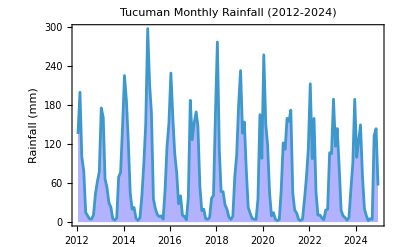

```mathematica
(* Extract monthly rainfall for Tucuman Province over 3 years *)
months = Flatten [ Table[
  {year, month},
  {year, 2012, 2024}, {month, 1, 12}
],1];

tucuGeom = GEEGeometry[bbox={-66.18, -28.02 ,-64.48, -26.13}];

monthlyRain = Table[
  Module[{startDate, endDate, expr, result},
    startDate = DateString[DateObject[{period[[1]], period[[2]], 1}],
      {"Year", "-", "Month", "-", "Day"}];
    endDate = DateString[DateObject[{period[[1]], period[[2]] + 1, 1}],
      {"Year", "-", "Month", "-", "Day"}];
    expr = GEECollection["UCSB-CHG/CHIRPS/DAILY"] //
      GEEFilterDate[startDate, endDate] //
      GEEFilterBounds[bbox] //
      GEESelectBands[{"precipitation"}] //
      GEECollectionSum //
      GEEReduceRegion[tucuGeom, "mean", 5000];
    result = GEECompute[expr];
    First[Values[result]]
  ],
  {period, months} 
];

(* Build a TimeSeries object *)
dates = DateObject[{#[[1]], #[[2]], 15}] & /@ months;
rainTS = TimeSeries[monthlyRain, {dates}];

(* Plot the raw monthly values *)
DateListPlot[rainTS,
  PlotLabel -> "Tucuman Monthly Rainfall (2012-2024)",
  AxesLabel -> {None, "Rainfall (mm)"},
  Filling -> Axis,
  FillingStyle -> Directive[Opacity[0.3], Blue]]
```

Apply smoothing and trend detection:

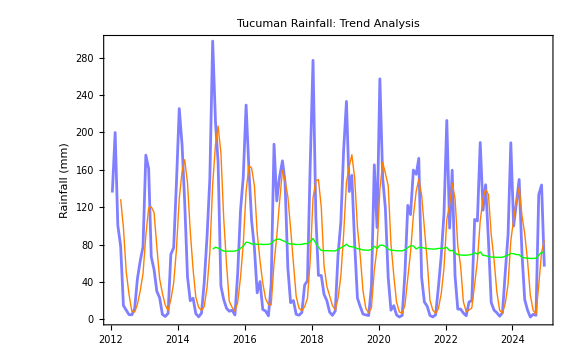

```mathematica
(* 3-month moving average to highlight seasonal cycles *)

smoothTS = MovingAverage[rainTS,Quantity[3,"Months"]];

annualTS=MovingAverage[rainTS,Quantity[3,"Year"]];

(* Combined visualization *)
Show[
  DateListPlot[rainTS,
    PlotStyle -> Directive[Opacity[0.5], Blue],
    PlotLabel -> "Tucuman Rainfall: Trend Analysis"],
  DateListPlot[smoothTS,
    PlotStyle -> Directive[Thick, Orange],
    Joined -> True],
   DateListPlot[annualTS,
    PlotStyle -> Directive[Thick, Green],
    Joined -> True],
  PlotLegends -> {"Monthly", "3-Month Moving Avg", "3-yr Moving Avg"},
  AxesLabel -> {None, "Rainfall (mm)"},PlotTheme->"Detailed",ImageSize->Large
]
```

## 3.3 Atmospheric Data

Atmospheric reanalysis products combine satellite observations with numerical weather models to produce spatially complete, temporally consistent records of key atmospheric variables.

## 3.3.1 ERA5-Land Reanalysis

ECMWF/ERA5_LAND/DAILY_AGGR provides daily aggregates of temperature, precipitation, wind, humidity, and pressure at approximately 11 km resolution. Its consistent methodology makes it well suited for climate trend studies.

Extract a temperature time series for a single point over one year:

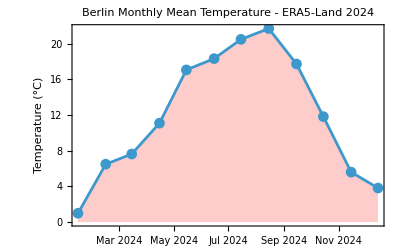

```mathematica
(* Monthly mean temperature for Berlin, 2024 *)
berlinPos = GeoPosition[{52.52, 13.40}];

monthlyTemp = Table[
  Module[{startDate, endDate, expr, result},
    startDate = DateString[DateObject[{2024, mo, 1}],
      {"Year", "-", "Month", "-", "Day"}];
    endDate = DateString[DateObject[{2024, mo + 1, 1}],
      {"Year", "-", "Month", "-", "Day"}];
    expr = GEECollection["ECMWF/ERA5_LAND/DAILY_AGGR"] //
      GEEFilterDate[startDate, endDate] //
      GEESelectBands[{"temperature_2m"}] //
      GEEMean //
      GEEAdd[-273.15];  (* Kelvin to Celsius *)
    result = GEEIdentify[berlinPos, expr];
    result["Values"][[1]]
  ],
  {mo, 1, 12}
];

dates = Table[DateObject[{2024, mo, 15}], {mo, 1, 12}];
tempTS = TimeSeries[monthlyTemp, {dates}];

DateListPlot[tempTS,
  PlotLabel -> "Berlin Monthly Mean Temperature - ERA5-Land 2024",
  AxesLabel -> {None, "Temperature (°C)"},
  Joined -> True,
  PlotMarkers -> Automatic,
  Filling -> 0,
  FillingStyle -> Directive[Opacity[0.2], Red],
  GridLines -> Automatic]
```

Wind speed map from u and v components:

Wind speed is not stored directly in ERA5; instead, the eastward (u10) and northward (v10) components are provided separately. Wind speed is the magnitude of the wind vector: sqrt(u^2 + v^2). The following example computes this entirely server-side using expression builder arithmetic.

```mathematica
(* January 2024 mean wind speed over Western Europe *)
u10 = GEECollection["ECMWF/ERA5_LAND/DAILY_AGGR"] //
  GEEFilterDate["2024-01-01", "2024-02-01"] //
  GEEFilterBounds[{-10.0, 35.0, 15.0, 60.0}] //
  GEESelectBands[{"u_component_of_wind_10m"}] //
  GEEMean //
  (* GEEMean appends _mean, producing "u_component_of_wind_10m_mean".
     GEERename then replaces it with "wind" so both components share
     a band name for arithmetic. *)
  GEERename[{"wind"}];

v10 = GEECollection["ECMWF/ERA5_LAND/DAILY_AGGR"] //
  GEEFilterDate["2024-01-01", "2024-02-01"] //
  GEEFilterBounds[{-10.0, 35.0, 15.0, 60.0}] //
  GEESelectBands[{"v_component_of_wind_10m"}] //
  GEEMean //
  GEERename[{"wind"}];

(* Wind speed = sqrt(u^2 + v^2) *)
uSquared = u10 // GEEPow[2];
vSquared = v10 // GEEPow[2];
windSpeed = GEEAdd[uSquared, vSquared] // GEESqrt;

GEEComputePixels[{-10.0, 35.0, 15.0, 60.0}, windSpeed,
  "VisParams" -> <|"min" -> 0, "max" -> 8,
    "palette" -> {"#ffffcc", "#c7e9b4", "#7fcdbb",
      "#41b6c4", "#1d91c0", "#225ea8", "#0c2c84"}|>,
  "ImageSize" -> {500, 500}]
(* Higher values along the North Sea and Atlantic coasts *)
```

-Graphics-

## 3.3.2 An Alternative Approach: GEEExpression for Wind Speed

When the arithmetic involves multiple bands from the same image, GEEExpression can be more concise than chaining individual math operators. This approach requires all bands in a single image, so the pipeline selects both components and uses the text expression syntax.

```mathematica
windExpr = GEECollection["ECMWF/ERA5_LAND/DAILY_AGGR"] //
  GEEFilterDate["2024-01-01", "2024-02-01"] //
  GEEFilterBounds[{-10.0, 35.0, 15.0, 60.0}] //
  GEESelectBands[{"u_component_of_wind_10m", "v_component_of_wind_10m"}] //
  GEEMean //
  GEEExpression["(u * u + v * v)**(0.5)", <|
    "u" -> "u_component_of_wind_10m_mean",
    "v" -> "v_component_of_wind_10m_mean"|>];

GEEComputePixels[{-10.0, 35.0, 15.0, 60.0}, windExpr,
  "VisParams" -> <|"min" -> 0, "max" -> 8,
    "palette" -> {"#ffffcc", "#c7e9b4", "#7fcdbb",
      "#41b6c4", "#1d91c0", "#225ea8", "#0c2c84"}|>,
  "ImageSize" -> {500, 500}]
```

-Graphics-

Note the _mean suffix on band names: GEEMean appends this suffix during collection reduction (see Section 3.3.1 note on band naming).

## 3.3.3 MODIS Aerosol Optical Depth

Aerosol optical depth (AOD) measures the amount of particulate matter in the atmosphere. High AOD values indicate pollution, dust storms, or wildfire smoke. MODIS/061/MCD19A2_GRANULES provides AOD at 1 km resolution.

```mathematica
aColors=<|GrayLevel[0]->"#000000",RGBColor[0, 0, 1]->"#0000ff",RGBColor[0.5, 0, 0.5]->"#800080",RGBColor[0, 1, 1]->"#00ffff",RGBColor[0, 1, 0]->"#00ff00",RGBColor[1, 1, 0]->"#ffff00",RGBColor[1, 0, 0]->"#ff0000"|>;
```

```mathematica
(* AOD over the Indo-Gangetic Plain during winter pollution season *)
aodExpr = GEECollection["MODIS/061/MCD19A2_GRANULES"] //
  GEEFilterDate["2024-11-01", "2025-01-01"] //
  GEEFilterBounds[{72.0, 10.0, 88.0, 30.0}] //
  GEESelectBands[{"Optical_Depth_047"}] //
  GEEMean ; 

GEEComputePixels[{72.0, 10.0, 88.0, 30.0}, aodExpr,
  "VisParams" -> <|"min" -> 0, "max" -> 1100,
    "palette" -> {"#000000","#0000ff","#800080","#00ffff","#00ff00","#ffff00","#ff0000"}|>,
  "ImageSize" -> {600, 600}]
(* Red/dark red over Delhi and the Gangetic Plain indicates severe pollution *)
```

-Graphics-

Query AOD at specific cities for comparison:

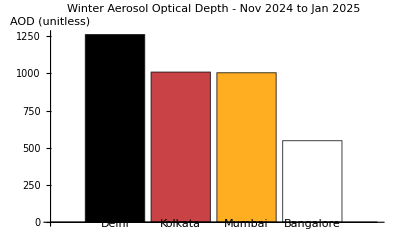

```mathematica
cities = <|
  "Delhi" -> GeoPosition[{28.61, 77.21}],
  "Kolkata" -> GeoPosition[{22.57, 88.36}],
  "Mumbai" -> GeoPosition[{19.08, 72.88}],
  "Bangalore" -> GeoPosition[{12.97, 77.59}]
|>;

aodValues = Association @ KeyValueMap[
  Function[{name, pos},
    name -> GEEIdentify[pos, aodExpr]["Values"][[1]]
  ],
  cities
];

BarChart[aodValues,
  ChartLabels -> Keys[aodValues],
  AxesLabel -> {None, "AOD (unitless)"},
  PlotLabel -> "Winter Aerosol Optical Depth - Nov 2024 to Jan 2025",
  ChartStyle -> "SunsetColors"]
```

## 3.4 Evapotranspiration

Evapotranspiration (ET) quantifies water loss from the land surface through soil evaporation and plant transpiration. It is a critical variable for agricultural water management, drought assessment, and hydrological modeling. For a complete watershed-scale water budget combining precipitation and ET, see Section 6.8.

## 3.4.1 MODIS Evapotranspiration

MODIS/061/MOD16A2 provides 8-day ET composites at 500 m resolution. The ET band stores values in units of kg/m^2/8-day (equivalent to mm/8-day); the scale factor is 0.1.

Map seasonal ET over an agricultural region:

```mathematica
(* Growing season ET for the California Central Valley *)
etExpr = GEECollection["MODIS/061/MOD16A2"] //
  GEEFilterDate["2024-04-01", "2024-10-01"] //
  GEEFilterBounds[{-122.0, 35.0, -119.0, 38.5}] //
  GEESelectBands[{"ET"}] //
  GEECollectionSum  //
GEEMultiply[0.1];  (*Scale to mm*);  (* Scale to mm *)

GEEComputePixels[{-122.0, 35.0, -119.0, 38.5}, etExpr,
  "VisParams" -> <|"min" -> 0, "max" -> 800,
    "palette" -> {"#ffffff","#fcd163","#99b718","#66a000","#3e8601","#207401","#056201","#004c00","#011301"}|>,
  "ImageSize" -> {500, 600}]
(* High ET over irrigated farmland, low ET over the Coast Ranges *)
```

-Graphics-

## 3.4.2 Irrigated vs. Rainfed Cropland ET Comparison

Use GEEReduceRegion on two different geometries to compare mean ET between irrigated and rainfed areas. This reveals the water demand differential driven by irrigation practices.

```mathematica
(* Define two geometries: irrigated and rainfed zones in the Central Valley *)
irrigatedGeom = GEEGeometry[{-120.8, 36.5, -120.4, 36.9}];  (* West side *)
rainfedGeom = GEEGeometry[{-119.8, 36.0, -119.4, 36.4}];    (* East foothills *)

(* Mean ET for each zone *)
irrigatedET = GEECompute[
  etExpr // GEEReduceRegion[irrigatedGeom, "mean", 500]
];
rainfedET = GEECompute[
  etExpr // GEEReduceRegion[rainfedGeom, "mean", 500]
];

Grid[{
  {"Zone", "Mean ET (mm/season)"},
  {"Irrigated", Round[First[Values[irrigatedET]], 1]},
  {"Rainfed", Round[First[Values[rainfedET]], 1]},
  {"Ratio", Round[
    First[Values[irrigatedET]] / First[Values[rainfedET]], 0.1]}
}, Frame -> All,
  Background -> {None, {LightBlue, None, None, None}}]
(* Irrigated areas typically show 2-3x higher ET than rainfed *)
```

Zone | Mean ET (mm/season)
Irrigated | 114
Rainfed | 147
Ratio | 0.8

## 3.4.3 Water Balance: Precipitation Minus Evapotranspiration

A simplified water balance model uses precipitation minus ET to estimate net water availability. Positive values indicate surplus (potential runoff or groundwater recharge); negative values indicate deficit (requiring irrigation or drawing from storage).

Server-side approach using GEESubtract:

```mathematica
(* Annual precipitation from CHIRPS (sum of daily values) *)
(* GEECollectionSum appends _sum to band names; rename to a common
   band name so GEESubtract can match bands between the two images *)
annualPrecip = GEECollection["UCSB-CHG/CHIRPS/DAILY"] //
  GEEFilterDate["2024-01-01", "2025-01-01"] //
  GEEFilterBounds[{-122.0, 35.0, -119.0, 38.5}] //
  GEESelectBands[{"precipitation"}] //
  GEECollectionSum //
  GEERename[{"annual_mm"}];

(* Annual ET from MODIS (sum of 8-day composites, scaled) *)
annualET = GEECollection["MODIS/061/MOD16A2"] //
  GEEFilterDate["2024-01-01", "2025-01-01"] //
  GEEFilterBounds[{-122.0, 35.0, -119.0, 38.5}] //
  GEESelectBands[{"ET"}] //
  GEECollectionSum //
  GEEMultiply[0.1] //
  GEERename[{"annual_mm"}];

(* Water balance = P - ET *)
waterBalance = GEESubtract[annualPrecip, annualET];

GEEComputePixels[{-122.0, 35.0, -119.0, 38.5}, waterBalance,
  "VisParams" -> <|"min" -> -500, "max" -> 500,
    "palette" -> {"#8c510a", "#d8b365", "#f6e8c3",
      "#f5f5f5", "#c7eae5", "#5ab4ac", "#01665e"}|>,
  "ImageSize" -> {500, 600}]
(* Brown = water deficit (ET > P), teal = water surplus (P > ET) *)
```

-Graphics-

Client-side approach using GEECompute results:

When you need the numeric values for further analysis in Wolfram Language, use GEEReduceRegion to extract regional means, then compute the balance client-side.

```mathematica
regionGeom = GEEGeometry[{-121.0, 36.0, -120.0, 37.0}];

precipMean = GEECompute[
  annualPrecip // GEEReduceRegion[regionGeom, "mean", 5000]
];
etMean = GEECompute[
  annualET // GEEReduceRegion[regionGeom, "mean", 500]
];

pVal = First[Values[precipMean]];
etVal = First[Values[etMean]];
balance = pVal - etVal;

Print["Precipitation: ", Round[pVal, 1], " mm/year"]
Print["Evapotranspiration: ", Round[etVal, 1], " mm/year"]
Print["Water Balance: ", Round[balance, 1], " mm/year"]
Print["Status: ", If[balance > 0, "Surplus", "Deficit"]]
```

Precipitation: 297 mm/year

Evapotranspiration: 292 mm/year

Water Balance: 5 mm/year

Status: Surplus

## 3.5 Multi-Year Climate Analysis

Longer time horizons reveal trends, periodicities, and climate shifts that single-year snapshots cannot capture. This section demonstrates decadal analysis workflows that combine GEE data extraction with Wolfram Language statistical and time series functions.

## 3.5.1 Decadal Temperature Trend

Extract annual mean land surface temperature for 10 years, fit a linear trend, and forecast future values.

```mathematica
(* Annual mean LST for a region near Madrid, 2014-2024 *)
madridGeom = GEEGeometry[{-3.8, 40.3, -3.5, 40.5}];
years = Range[2014, 2024];

annualLST = Table[
  Module[{startDate, endDate, expr, result},
    startDate = ToString[yr] <> "-01-01";
    endDate = ToString[yr + 1] <> "-01-01";
    expr = GEECollection["MODIS/061/MOD11A2"] //
      GEEFilterDate[startDate, endDate] //
      GEEFilterBounds[{-3.8, 40.3, -3.5, 40.5}] //
      GEESelectBands[{"LST_Day_1km"}] //
      GEEMean //
      GEEMultiply[0.02] //
      GEEAdd[-273.15] //
      GEEReduceRegion[madridGeom, "mean", 1000];
    result = GEECompute[expr];
    First[Values[result]]
  ],
  {yr, years}
];

(* Build TimeSeries *)
dates = DateObject[{#, 7, 1}] & /@ years;
lstTS = TimeSeries[annualLST, {dates}];

(* Linear trend fit *)
lm = LinearModelFit[
  Transpose[{years, annualLST}],
  x, x];

(* Forecast 5 years ahead *)
futureYears = Range[2025, 2029];
forecast = lm /@ futureYears;

(* Visualization with confidence bands *)
Show[
  ListPlot[Transpose[{years, annualLST}],
    PlotStyle -> {PointSize[0.015], Blue},
    PlotLabel -> "Madrid Decadal LST Trend (2014-2024)"],
  Plot[{
      lm[x],
      lm[x] + 2 * lm["EstimatedVariance"]^0.5,
      lm[x] - 2 * lm["EstimatedVariance"]^0.5
    }, {x, 2014, 2029},
    PlotStyle -> {
      Directive[Thick, Red],
      Directive[Thin, Dashed, Red],
      Directive[Thin, Dashed, Red]},
    Filling -> {2 -> {3}}],
  ListPlot[Transpose[{futureYears, forecast}],
    PlotStyle -> {PointSize[0.012], Red, Opacity[0.5]}],
  AxesLabel -> {"Year", "Mean LST (°C)"},
  PlotRange -> All,
  GridLines -> Automatic
]

(* Report the trend *)
slope = lm["BestFitParameters"][[2]];
Print["Warming rate: ", Round[slope, 0.01], " °C/year"]
Print["R-squared: ", Round[lm["RSquared"], 0.001]]
```

## 3.5.2 Time Series Forecasting

Use Wolfram Language's TimeSeriesForecast for a model-based projection that accounts for seasonality.

```mathematica
(* Monthly LST time series for 5 years *)
monthlyLST = Flatten @ Table[
  Module[{startDate, endDate, expr, result},
    startDate = DateString[DateObject[{yr, mo, 1}],
      {"Year", "-", "Month", "-", "Day"}];
    endDate = DateString[DateObject[{yr, mo + 1, 1}],
      {"Year", "-", "Month", "-", "Day"}];
    expr = GEECollection["MODIS/061/MOD11A2"] //
      GEEFilterDate[startDate, endDate] //
      GEEFilterBounds[{-3.8, 40.3, -3.5, 40.5}] //
      GEESelectBands[{"LST_Day_1km"}] //
      GEEMean //
      GEEMultiply[0.02] //
      GEEAdd[-273.15] //
      GEEReduceRegion[madridGeom, "mean", 1000];
    result = GEECompute[expr];
    First[Values[result]]
  ],
  {yr, 2020, 2024}, {mo, 1, 12}
];

monthDates = Flatten @ Table[
  DateObject[{yr, mo, 15}],
  {yr, 2020, 2024}, {mo, 1, 12}
];
lstMonthlyTS = TimeSeries[monthlyLST, {monthDates}];

(* Forecast 12 months ahead *)
forecastTS = TimeSeriesForecast[lstMonthlyTS, 12];

DateListPlot[{lstMonthlyTS, forecastTS},
  PlotLegends -> {"Observed", "Forecast"},
  PlotLabel -> "Madrid Monthly LST with 12-Month Forecast",
  AxesLabel -> {None, "LST (°C)"},
  PlotStyle -> {Blue, Directive[Dashed, Red]}]
```

## 3.5.3 Drought Monitoring with Standardized Precipitation Index

The Standardized Precipitation Index (SPI) transforms precipitation data into a standardized metric where negative values indicate drought. This simplified implementation computes monthly precipitation z-scores using the long-term mean and standard deviation.

```mathematica
(* Monthly precipitation for a drought-prone region over 10 years *)
regionGeom = GEEGeometry[{-5.5, 36.5, -4.5, 37.5}];  (* Southern Spain *)

monthlyPrecip = Flatten @ Table[
  Module[{startDate, endDate, expr, result},
    startDate = DateString[DateObject[{yr, mo, 1}],
      {"Year", "-", "Month", "-", "Day"}];
    endDate = DateString[DateObject[{yr, mo + 1, 1}],
      {"Year", "-", "Month", "-", "Day"}];
    expr = GEECollection["UCSB-CHG/CHIRPS/DAILY"] //
      GEEFilterDate[startDate, endDate] //
      GEEFilterBounds[{-5.5, 36.5, -4.5, 37.5}] //
      GEESelectBands[{"precipitation"}] //
      GEECollectionSum //
      GEEReduceRegion[regionGeom, "mean", 5000];
    result = GEECompute[expr];
    First[Values[result]]
  ],
  {yr, 2015, 2024}, {mo, 1, 12}
];

(* Compute SPI-like z-scores by month *)
(* Group values by calendar month to compute monthly climatology *)
byMonth = Table[
  monthlyPrecip[[mo ;; ;; 12]],  (* Every value for this calendar month *)
  {mo, 1, 12}
];
monthMeans = Mean /@ byMonth;
monthStdDevs = StandardDeviation /@ byMonth;

spi = Table[
  Module[{mo, idx},
    idx = Mod[i - 1, 12] + 1;
    If[monthStdDevs[[idx]] == 0, 0,
      (monthlyPrecip[[i]] - monthMeans[[idx]]) / monthStdDevs[[idx]]
    ]
  ],
  {i, Length[monthlyPrecip]}
];

(* Classify drought severity *)
(* SPI categories: >= 2.0 extremely wet, 1.5-2.0 very wet, 1.0-1.5 moderately wet,
   -1.0 to 1.0 near normal, -1.0 to -1.5 moderately dry,
   -1.5 to -2.0 severely dry, <= -2.0 extremely dry *)

spiDates = Flatten @ Table[
  DateObject[{yr, mo, 15}],
  {yr, 2015, 2024}, {mo, 1, 12}
];
spiTS = TimeSeries[spi, {spiDates}];

(* Color-coded drought plot *)
DateListPlot[spiTS,
  PlotLabel -> "Standardized Precipitation Index - Southern Spain (2015-2024)",
  AxesLabel -> {None, "SPI"},
  Filling -> 0,
  ColorFunction -> Function[{x, y},
    Which[
      y < -2, Darker[Red],
      y < -1.5, Red,
      y < -1, Orange,
      y > 1.5, Darker[Blue],
      y > 1, Blue,
      True, Gray
    ]],
  ColorFunctionScaling -> False,
  PlotRange -> {All, {-3, 3}},
  GridLines -> {None, {-2, -1.5, -1, 1, 1.5, 2}},
  GridLinesStyle -> Directive[Dashed, GrayLevel[0.7]],
  Epilog -> {
    Text[Style["Extremely Dry", 8, Red], Scaled[{0.95, 0.05}], {1, 0}],
    Text[Style["Extremely Wet", 8, Blue], Scaled[{0.95, 0.95}], {1, 0}]
  }]
```

## 3.5.4 Detecting Seasonal Cycles with Fourier Analysis

Wolfram Language's Fourier and Periodogram functions reveal dominant periodicities in climate time series. A monthly temperature series should show a strong 12-month cycle.

```mathematica
(* Use the monthly LST time series from Section 3.5.2 *)
(* Compute the power spectrum *)
Periodogram[lstMonthlyTS["Values"],
  PlotLabel -> "LST Power Spectrum - Madrid",
  PlotRange -> All,
  ScalingFunctions -> "Log"]

(* The dominant peak near frequency 1/12 confirms the annual cycle *)
(* A secondary peak at 1/6 (semiannual) may also appear due to the
   bimodal temperature distribution in continental climates *)

(* Extract the dominant period *)
ft = Abs[Fourier[lstMonthlyTS["Values"]]]^2;
freqs = Range[0, Length[ft] - 1] / Length[ft];
peakIdx = Ordering[ft[[2 ;; Floor[Length[ft]/2]]], -1][[1]] + 1;
dominantPeriod = Length[ft] / (peakIdx - 1);
Print["Dominant period: ", Round[dominantPeriod, 0.1], " months"]
(* Expected: ~12 months *)
```

## 3.6 Solar Radiation

Solar radiation drives the surface energy budget and is critical for solar energy site assessment. Combining Wolfram Language's astronomical functions with GEE terrain data enables physically based irradiance estimation.

## 3.6.1 Solar Geometry with Wolfram Language

The built-in SunPosition function computes solar altitude and azimuth for any location and time, which determines how much direct sunlight reaches a tilted surface.

```mathematica
(* Solar position at noon on the summer solstice in Austin, TX *)
pos = GeoPosition[{30.27, -97.74}];
date = DateObject[{2024, 6, 21, 12, 0, 0}, TimeZone -> -5];

sunPos = SunPosition[pos, date];
altitude = QuantityMagnitude[sunPos[[1]], "AngularDegrees"];
azimuth = QuantityMagnitude[sunPos[[2]], "AngularDegrees"];

Print["Solar altitude: ", Round[altitude, 0.1], "°"]
Print["Solar azimuth: ", Round[azimuth, 0.1], "°"]

(* Daily solar trajectory *)
times = Table[
  DateObject[{2024, 6, 21, h, 0, 0}, TimeZone -> -5],
  {h, 6, 20, 0.5}
];
trajectory = Table[
  Module[{sp},
    sp = SunPosition[pos, t];
    {QuantityMagnitude[sp[[2]], "AngularDegrees"],
     QuantityMagnitude[sp[[1]], "AngularDegrees"]}
  ],
  {t, times}
];

ListLinePlot[trajectory,
  PlotLabel -> "Solar Trajectory - Austin, TX (Summer Solstice)",
  AxesLabel -> {"Azimuth (°)", "Altitude (°)"},
  PlotRange -> {{0, 360}, {0, 90}},
  AspectRatio -> 1/3,
  PlotMarkers -> Automatic]
```

## 3.6.2 Terrain-Adjusted Solar Irradiance

Slope and aspect from GEE terrain data determine how a surface is oriented relative to incoming sunlight. South-facing slopes in the Northern Hemisphere receive more direct radiation than north-facing slopes.

```mathematica
(* Compute terrain from SRTM DEM *)
dem = GEELoadImage["USGS/SRTMGL1_003"];
terrain = GEETerrain[dem];

(* Sample slope and aspect at a mountain location *)
mountainPos = GeoPosition[{39.75, -105.25}];  (* Rocky Mountain foothills *)
terrainVals = GEEIdentify[mountainPos, terrain];

(* GEETerrain produces bands: elevation, slope, aspect, hillshade *)
Print["Terrain at sample point:"]
MapThread[
  Print["  ", #1, ": ", #2] &,
  {terrainVals["Bands"], terrainVals["Values"]}
]
```

Estimate clear-sky solar irradiance on a tilted surface:

```mathematica
(* Solar constant (W/m^2) *)
solarConstant = 1361;

(* Sample terrain across a mountain transect *)
transectPoints = Table[
  GeoPosition[{39.75, lon}],
  {lon, -105.40, -105.10, 0.03}
];
terrainSamples = GEEGetSamples[transectPoints, terrain];

(* Compute solar angle at noon, summer solstice *)
solarAlt = QuantityMagnitude[
  SunPosition[GeoPosition[{39.75, -105.25}],
    DateObject[{2024, 6, 21, 12, 0, 0}, TimeZone -> -6]][[1]],
  "AngularDegrees"];
solarAz = QuantityMagnitude[
  SunPosition[GeoPosition[{39.75, -105.25}],
    DateObject[{2024, 6, 21, 12, 0, 0}, TimeZone -> -6]][[2]],
  "AngularDegrees"];

(* Compute irradiance on tilted surfaces *)
(* Bands are alphabetical: aspect, elevation, hillshade, slope *)
irradiance = Table[
  Module[{vals, aspect, slope, cosIncidence, irr},
    vals = terrainSamples[[i]]["Values"];
    (* Band order from GEETerrain: aspect, elevation, hillshade, slope *)
    aspect = vals[[1]] * Pi / 180;   (* Convert to radians *)
    slope = vals[[4]] * Pi / 180;
    (* Cosine of incidence angle between sun vector and surface normal *)
    cosIncidence = Sin[solarAlt * Pi / 180] * Cos[slope] +
      Cos[solarAlt * Pi / 180] * Sin[slope] *
      Cos[(solarAz - vals[[1]]) * Pi / 180];
    irr = solarConstant * Max[0, cosIncidence] * 0.75;  (* 0.75 atmospheric transmittance *)
    irr
  ],
  {i, Length[terrainSamples]}
];

ListLinePlot[
  Transpose[{Range[Length[irradiance]], irradiance}],
  PlotLabel -> "Estimated Solar Irradiance Along Mountain Transect",
  AxesLabel -> {"Transect Point", "Irradiance (W/m\[TwoSuperior])"},
  Filling -> Bottom,
  FillingStyle -> Directive[Opacity[0.3], Yellow],
  PlotRange -> {0, All}]
```

## 3.6.3 Hillshade Visualization

GEE's GEETerrain also computes hillshade (simulated shadow pattern) which provides an intuitive view of terrain relief. Combining hillshade with elevation creates publication-quality terrain maps.

```mathematica
(* Hillshade map of the Colorado Rockies *)
terrainImg = GEETerrain[GEELoadImage["USGS/SRTMGL1_003"]];

(* Select just the hillshade band *)
hillshade = terrainImg // GEESelectBands[{"hillshade"}];

GEEComputePixels[{-106.0, 39.0, -105.0, 40.0}, hillshade,
  "VisParams" -> <|"min" -> 0, "max" -> 255|>,
  "ImageSize" -> {512, 512}]
```

## 3.7 Putting It All Together: Multi-Variable Climate Dashboard

This final section demonstrates how to combine multiple climate variables into a unified analysis. The workflow extracts temperature, precipitation, ET, and wind data for a single region and present them as an integrated dashboard.

```mathematica
(* Define the study region: Central Spain *)
region = {-4.0, 39.5, -3.0, 40.5};
regionGeom = GEEGeometry[region];
studyPoint = GeoPosition[{40.0, -3.5}];

(* --- Temperature from ERA5 --- *)
tempData = Table[
  Module[{s, e, expr, result},
    s = DateString[DateObject[{2024, mo, 1}], {"Year", "-", "Month", "-", "Day"}];
    e = DateString[DateObject[{2024, mo + 1, 1}], {"Year", "-", "Month", "-", "Day"}];
    expr = GEECollection["ECMWF/ERA5_LAND/DAILY_AGGR"] //
      GEEFilterDate[s, e] //
      GEESelectBands[{"temperature_2m"}] //
      GEEMean //
      GEEAdd[-273.15];
    result = GEEIdentify[studyPoint, expr];
    result["Values"][[1]]
  ],
  {mo, 1, 12}
];

(* --- Precipitation from CHIRPS --- *)
precipData = Table[
  Module[{s, e, expr, result},
    s = DateString[DateObject[{2024, mo, 1}], {"Year", "-", "Month", "-", "Day"}];
    e = DateString[DateObject[{2024, mo + 1, 1}], {"Year", "-", "Month", "-", "Day"}];
    expr = GEECollection["UCSB-CHG/CHIRPS/DAILY"] //
      GEEFilterDate[s, e] //
      GEEFilterBounds[region] //
      GEESelectBands[{"precipitation"}] //
      GEECollectionSum //
      GEEReduceRegion[regionGeom, "mean", 5000];
    result = GEECompute[expr];
    First[Values[result]]
  ],
  {mo, 1, 12}
];

(* --- Evapotranspiration from MODIS --- *)
etData = Table[
  Module[{s, e, expr, result},
    s = DateString[DateObject[{2024, mo, 1}], {"Year", "-", "Month", "-", "Day"}];
    e = DateString[DateObject[{2024, mo + 1, 1}], {"Year", "-", "Month", "-", "Day"}];
    expr = GEECollection["MODIS/061/MOD16A2"] //
      GEEFilterDate[s, e] //
      GEEFilterBounds[region] //
      GEESelectBands[{"ET"}] //
      GEECollectionSum //
      GEEMultiply[0.1] //
      GEEReduceRegion[regionGeom, "mean", 500];
    result = GEECompute[expr];
    First[Values[result]]
  ],
  {mo, 1, 12}
];

(* --- Build dashboard --- *)
months = Table[DateObject[{2024, mo, 15}], {mo, 1, 12}];

tempTS = TimeSeries[tempData, {months}];
precipTS = TimeSeries[precipData, {months}];
etTS = TimeSeries[etData, {months}];
waterBalanceTS = TimeSeries[precipData - etData, {months}];

Grid[{
  {
    DateListPlot[tempTS,
      PlotLabel -> "Temperature (°C)",
      PlotStyle -> Red, Joined -> True, PlotMarkers -> Automatic,
      ImageSize -> 350],
    DateListPlot[precipTS,
      PlotLabel -> "Precipitation (mm)",
      Filling -> Axis, FillingStyle -> Directive[Opacity[0.3], Blue],
      ImageSize -> 350]
  },
  {
    DateListPlot[etTS,
      PlotLabel -> "Evapotranspiration (mm)",
      PlotStyle -> Darker[Green], Joined -> True, PlotMarkers -> Automatic,
      ImageSize -> 350],
    DateListPlot[waterBalanceTS,
      PlotLabel -> "Water Balance: P - ET (mm)",
      Filling -> 0,
      ColorFunction -> Function[{x, y}, If[y > 0, Blue, Red]],
      ColorFunctionScaling -> False,
      ImageSize -> 350]
  }
}, Spacings -> {1, 1},
  Frame -> All,
  Background -> White]
```

Compute annual summary statistics:

```mathematica
annualSummary = <|
  "Mean Temperature" ->
    Row[{Round[Mean[tempData], 0.1], " °C"}],
  "Total Precipitation" ->
    Row[{Round[Total[precipData], 1], " mm"}],
  "Total ET" ->
    Row[{Round[Total[etData], 1], " mm"}],
  "Annual Water Balance" ->
    Row[{Round[Total[precipData] - Total[etData], 1], " mm"}],
  "Wettest Month" ->
    DateString[months[[Ordering[precipData, -1][[1]]]],
      {"MonthName"}],
  "Driest Month" ->
    DateString[months[[Ordering[precipData, 1][[1]]]],
      {"MonthName"}],
  "Hottest Month" ->
    DateString[months[[Ordering[tempData, -1][[1]]]],
      {"MonthName"}]
|>;

Dataset[annualSummary]
```

## Summary

Scale factors matter. Most climate products store values as scaled integers for compression. Always check the dataset documentation and apply the correct scale factor (GEEMultiply) and offset (GEEAdd) before interpreting values.

Server-side vs. client-side processing. Use server-side arithmetic (GEEMultiply, GEEAdd, GEESubtract, GEEExpression) when you need to produce maps or process large regions. Use client-side computation when you need fine-grained statistical analysis with Wolfram Language tools (LinearModelFit, TimeSeries, Fourier).

The // pipeline is composable. Each expression builder returns an expression tree that can be passed to any consumer function. Build reusable pipeline fragments and combine them:

```mathematica
(* Reusable CHIRPS monthly sum builder *)
chirpsMonthlySum[startDate_, endDate_, bbox_] :=
  GEECollection["UCSB-CHG/CHIRPS/DAILY"] //
    GEEFilterDate[startDate, endDate] //
    GEEFilterBounds[bbox] //
    GEESelectBands[{"precipitation"}] //
    GEECollectionSum;
```

GEEReduceRegion bridges server and client. It computes a spatial statistic on the server and returns a single number, which is the natural interface point for Wolfram Language time series analysis.

Band name suffixes. GEEMean appends _mean and GEEMedian appends _median to band names. When using GEEExpression after an aggregation step, reference the suffixed names (e.g., "temperature_2m_mean").

Wolfram Language statistical tools complement GEE. Functions like TimeSeries, MovingAverage, LinearModelFit, TimeSeriesForecast, Periodogram, and Fourier add analytical depth that the GEE API alone cannot provide.

## Quick Reference: Datasets Used in This Chapter

## Quick Reference: Key Functions Used in This Chapter

Next: Chapter 4: Terrain and Geophysical Analysis